```mathematica
files = FileNames["*.tab"];
datas = Import[#]&/@ files;
datas = Drop[#, 1]&/@ datas;
A=Transpose[{#[[All,1]],#[[All,2]]}]&/@ datas;
B=Transpose[{#[[All,1]],#[[All,3]]}]&/@ datas;
ABs = Transpose[{A, B}];
```

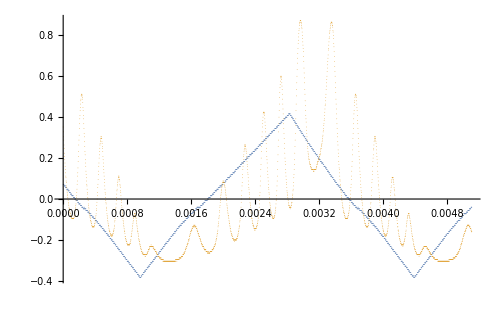
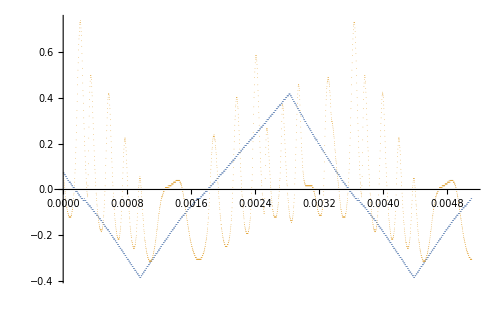
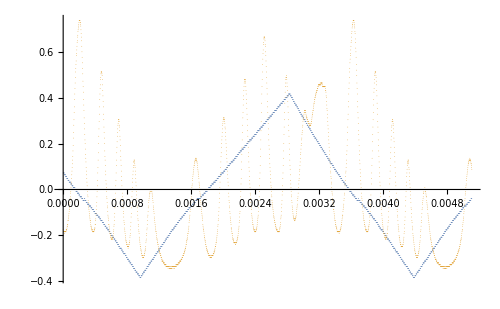
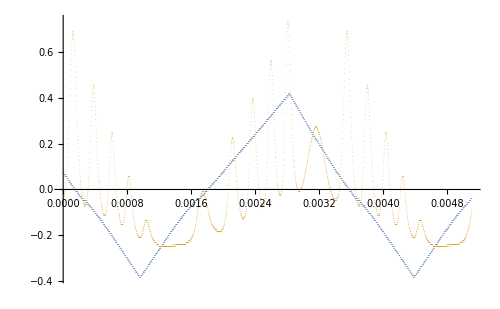
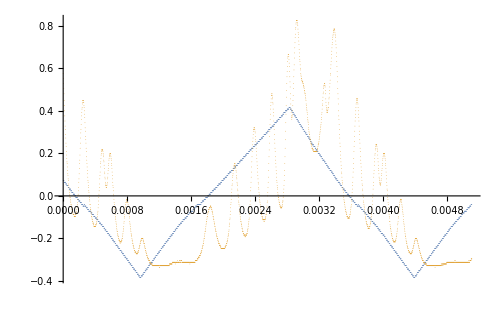
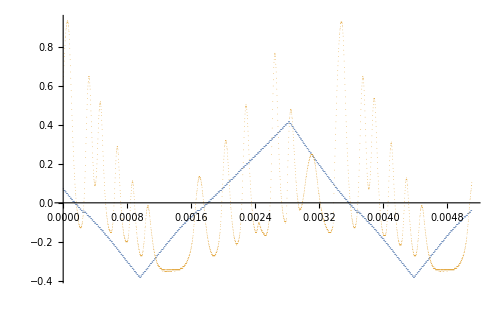
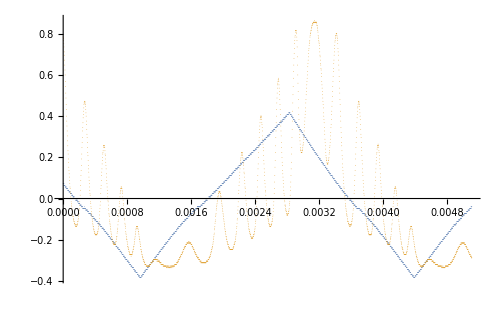
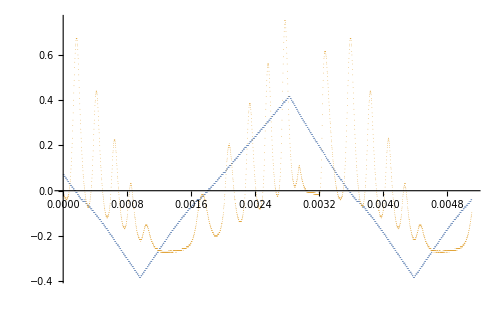

```mathematica
ListPlot[#, ImageSize->500,PlotStyle->{PointSize[0.0001]}, PlotRange->All]&/@ ABs
```

```mathematica
ch1 = ABs[[1, 1]];
ch2 = ABs[[1, 2]];
```